```mathematica
θ=π/4
```

```mathematica
l'angolo compreso tra i due lati è
π+FullSimplify [ArcTan[(Sin[θ]-1)/Cos[θ]]-(π/2+θ)]
```

angolo compreso due è i lati tra l'

π/8

```mathematica
ϕ=π+FullSimplify[ArcTan[(Sin[θ]-1)/Cos[θ]]]
```

(7 π)/8

```mathematica
{ColorSlider[Dynamic[x]],Dynamic[x]}
```

{$CellContext`x,}

```mathematica
Graphics[{EdgeForm[Thick],RGBColor[1.,0.7408255130846113,0.37500572213321126],Polygon[{{Cos[θ],Sin[θ]-1},{0,1/Sin[θ]-1},{-Cos[θ],Sin[θ]-1},{0,0}}]}]
```

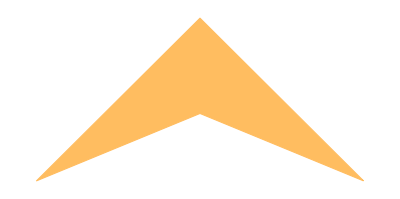

-Graphics-

```mathematica
Graphics[{EdgeForm[Thick],LightBlue,Polygon[{{Cos[θ],Sin[θ]-1},{0,1/Sin[θ]-1},{-Cos[θ],Sin[θ]-1},{0,0}}],,Blue,Circle[{Cos[θ],Sin[θ]-1},0.3,{ϕ,π-θ}],Circle[{0,1/Sin[θ]-1},0.2,{π+π/4,2π-π/4}],Circle[{0,0},0.2,{-π/8,π+π/8}],Circle[{-Cos[θ],Sin[θ]-1},0.3,{π/8,θ}]}]
```

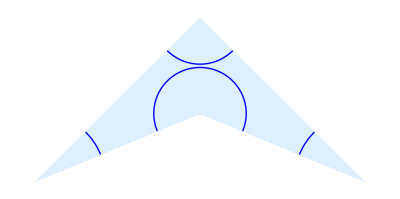

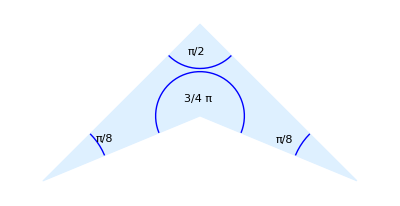

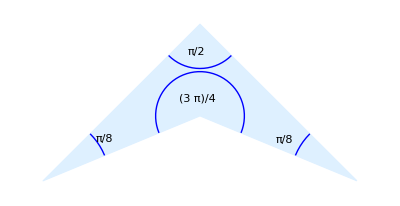

```mathematica
FullSimplify[π+ArcTan[(Sin[θ]-1)/Cos[θ]]-(π/2+θ),0<θ<π/2]
```

π/8

```mathematica
Tan[ϕ- π/2]
```

-Cot[ϕ]